```mathematica
Remove["Global`*"]
```

# Chi Matrix FOC5-3rd run

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of either
	- a 2D shape with an area proportional to |cij| or given by the optianl function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optianl function  functionForArrowLength(cij);
	- both 2D shape and arrow as defined above.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	- drawFrame: True (default) or False. Draw a black square around each matrix cell
	- frameFaceFunction: function of the position ij returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
	- showCentralPoint: True or False (default) wether to draw a central point in the cell.
	- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	- show2DShape: True (default) or False. Wether to draw the 2D shape or not.
	- whatShape: "circle" (default) or "square".
	- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
	- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
	- borderColor: Color of the 2D shape border (default is Black).
	- fill2DShape: Wether to fill the 2Dshape (default is True);
	- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π . 
	- thicknessShape: thickness of the shape border (default is 0.01, i.e 1% of the cell).
	- showArrow:  True (default) or False. Wether to draw the arrow or not.
	- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
	- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
	- thicknessArrow: thickness of the arrow border (default is 0.01, i.e 1% of the whole graph).
	- arrowColor: Color of the arow (default is Black).
	- arrowSize: Size of the arrow in fraction of the whole graph  (default is 0.05, i.e. 5%).

```mathematica
Options[myPlotElement]=
{
drawFrame->True,frameFaceFunction->({White,Opacity[0]}&),
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,thicknessShape->.001,borderColor->Black,fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,thicknessArrow->.001,arrowSize->.05,arrowColor->Black,
showCentralPoint->False,centralPointSize->Small
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=(position-0.5{1,1}),
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={}
},
If[OptionValue[drawFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[{Thickness[OptionValue[thicknessShape]],OptionValue[borderColor]}],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow={OptionValue[arrowColor],Thickness[OptionValue[thicknessArrow]],Arrowheads[OptionValue[arrowSize]],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]}];
Graphics[frame~Join~shape~Join~arrow~Join~centralPoint]];
ComplexMatrixDraw[number_?NumberQ,opts___]:=ComplexMatrixDraw[{{number}},opts];
ComplexMatrixDraw[vector_?VectorQ,opts___]:=ComplexMatrixDraw[List/@vector,opts];
ComplexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,(Reverse[#2]-{1,1}){1,-1},opts]&,matrix,{2}]];
```

### iSWAP gata tomography F0-C5

```mathematica
replacements={"j"->"ⅈ","e"->"*10^"};
myImport[fileName_,type_,headerLines_:0,printHeader_:False]:=
Block[
{data=Import[fileName,type],depth},
depth=data//dimensions//Length;
If[printHeader,Print["Header: "<>ToString[Take[data,headerLines]]]];
data=(Map[StringReplace[#,replacements]&,Drop[data,headerLines],{depth}])// ToExpression
]
```

```mathematica
(χideal={{1/8 (3+2 √2),0,0,0,0,1/8 ⅈ (1+√2),0,0,0,0,-1/8 ⅈ (1+√2),0,0,0,0,1/8},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8 ⅈ (1+√2),0,0,0,0,1/8,0,0,0,0,-1/8,0,0,0,0,-1/8 ⅈ (-1+√2)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8 ⅈ (1+√2),0,0,0,0,-1/8,0,0,0,0,1/8,0,0,0,0,1/8 ⅈ (-1+√2)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,0,0,0,1/8 ⅈ (-1+√2),0,0,0,0,-1/8 ⅈ (-1+√2),0,0,0,0,1/8 (3-2 √2)}})//MatrixForm
χideal2=MapIndexed[Take[#1,#2[[1]]]&,χideal,1];
```

(1/8 (3+2 √2) | 0 | 0 | 0 | 0 | 1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | 1/8 (3-2 √2))

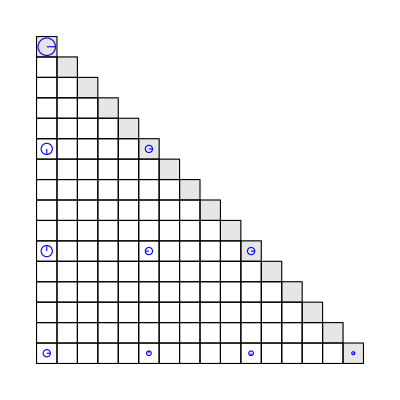

```mathematica
gr0=ComplexMatrixDraw[χideal2,borderColor->Blue,arrowColor->Blue,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.002, thicknessArrow->0.002,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)]
```

```mathematica
{χ,χPhys}=Partition[#,16]&/@(myImport["L:\\local-expdata\\FO-C5\\3rd-Run\\2011_04_21\\Quantum Process Tomography at 31 ns-16-chi matrix-3.txt","Table",1]//Chop);
χPhys2=MapIndexed[Take[#1,#2[[1]]]&,χPhys,1];
```

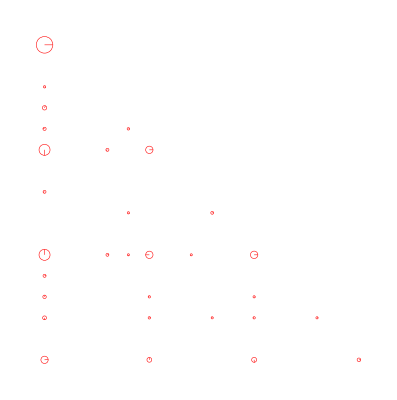

```mathematica
gr1=ComplexMatrixDraw[χPhys2,borderColor->Red,arrowColor->Red,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&),drawFrame->False]
```

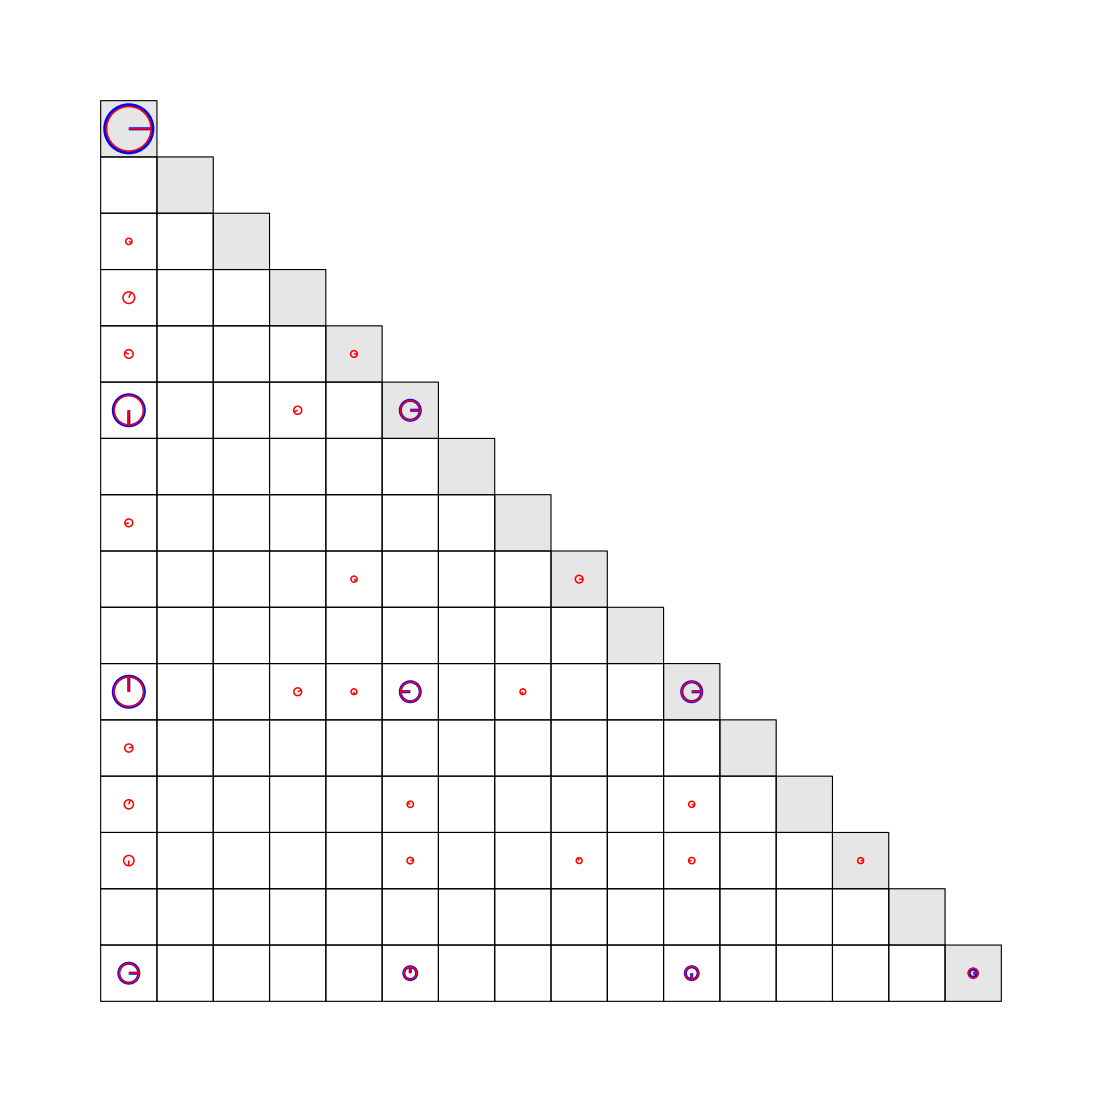

```mathematica
Show[gr0,gr1]
```

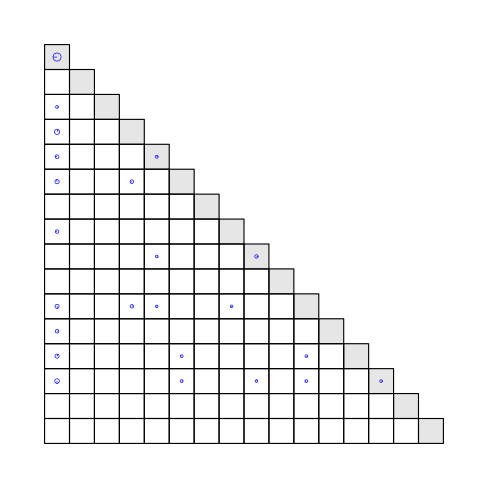

```mathematica
χError=χPhys2-χideal2;
ComplexMatrixDraw[χError,borderColor->Blue,arrowColor->Blue,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&),frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)]
```

### Density matrices Grover

#### Density matrix as a function of Pauli Set

```mathematica
Clear[x,y,z,i];
opBase1={x,y,z,i};
opBase2=Outer[KroneckerProduct,opBase1,opBase1]//Flatten
rule1=(KroneckerProduct[op1_,op2_]:>ToExpression[ToString[op1]<>ToString[op2]]);
pauliSet=opBase2/.rule1; "Pauli set is "<>ToString[pauliSet]
x={{0,1},{1,0}};y={{0,-ⅈ},{ⅈ,0}};z={{1,0},{0,-1}};i={{1,0},{0,1}};
ρM=Table[ρ[i,j],{i,4},{j,4}];
pauliSetTh=FullSimplify[Tr[#.ρM]&/@opBase2];
sys=#==0&/@(pauliSet-pauliSetTh);
ρS=ρM/.(Solve[sys,ρM//Flatten]//Flatten);
"ρS="MatrixForm[ρS]
Clear[x,y,z,i];
```

{KroneckerProduct[x,x],KroneckerProduct[x,y],KroneckerProduct[x,z],KroneckerProduct[x,i],KroneckerProduct[y,x],KroneckerProduct[y,y],KroneckerProduct[y,z],KroneckerProduct[y,i],KroneckerProduct[z,x],KroneckerProduct[z,y],KroneckerProduct[z,z],KroneckerProduct[z,i],KroneckerProduct[i,x],KroneckerProduct[i,y],KroneckerProduct[i,z],KroneckerProduct[i,i]}

Pauli set is {xx, xy, xz, xi, yx, yy, yz, yi, zx, zy, zz, zi, ix, iy, iz, ii}

ρS= (1/4 (ii+iz+zi+zz) | 1/4 (ix-ⅈ iy+zx-ⅈ zy) | 1/4 (xi+xz-ⅈ yi-ⅈ yz) | 1/4 (xx-ⅈ xy-ⅈ yx-yy)
1/4 (ix+ⅈ iy+zx+ⅈ zy) | 1/4 (ii-iz+zi-zz) | 1/4 (xx+ⅈ xy-ⅈ yx+yy) | 1/4 (xi-xz-ⅈ yi+ⅈ yz)
1/4 (xi+xz+ⅈ yi+ⅈ yz) | 1/4 (xx-ⅈ xy+ⅈ yx+yy) | 1/4 (ii+iz-zi-zz) | 1/4 (ix-ⅈ iy-zx+ⅈ zy)
1/4 (xx+ⅈ xy+ⅈ yx-yy) | 1/4 (xi-xz+ⅈ yi-ⅈ yz) | 1/4 (ix+ⅈ iy-zx-ⅈ zy) | 1/4 (ii-iz-zi+zz))

```mathematica
ρM
pauliSet
```

{{ρ[1,1],ρ[1,2],ρ[1,3],ρ[1,4]},{ρ[2,1],ρ[2,2],ρ[2,3],ρ[2,4]},{ρ[3,1],ρ[3,2],ρ[3,3],ρ[3,4]},{ρ[4,1],ρ[4,2],ρ[4,3],ρ[4,4]}}

{xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

```mathematica
ρ={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
meas={xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
id={{1,0},{0,1}};
measure=FullSimplify[Tr[#.ρ]&/@opBase2];
```

#### Ideal density matrices

{(1/4 | -1/4 | -1/4 | -1/4
-1/4 | 1/4 | 1/4 | 1/4
-1/4 | 1/4 | 1/4 | 1/4
-1/4 | 1/4 | 1/4 | 1/4),(1/4 | -1/4 | 1/4 | 1/4
-1/4 | 1/4 | -1/4 | -1/4
1/4 | -1/4 | 1/4 | 1/4
1/4 | -1/4 | 1/4 | 1/4),(1/4 | 1/4 | -1/4 | 1/4
1/4 | 1/4 | -1/4 | 1/4
-1/4 | -1/4 | 1/4 | -1/4
1/4 | 1/4 | -1/4 | 1/4),(1/4 | 1/4 | 1/4 | -1/4
1/4 | 1/4 | 1/4 | -1/4
1/4 | 1/4 | 1/4 | -1/4
-1/4 | -1/4 | -1/4 | 1/4)}

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

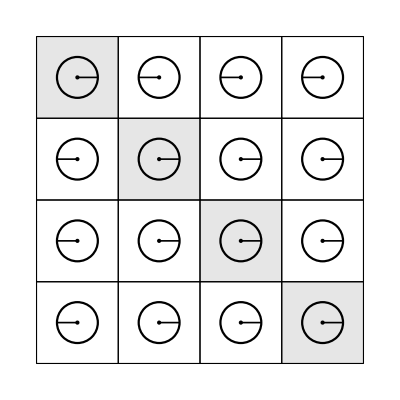
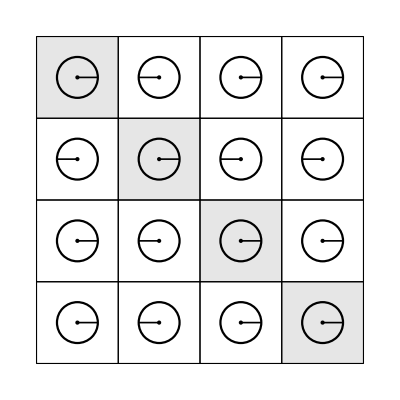
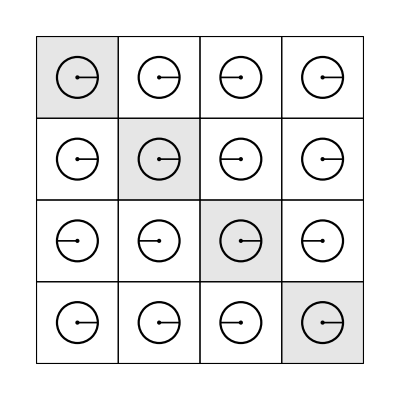
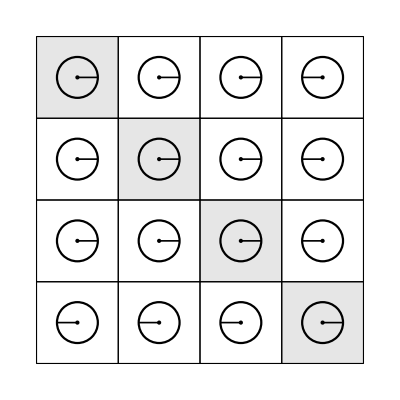

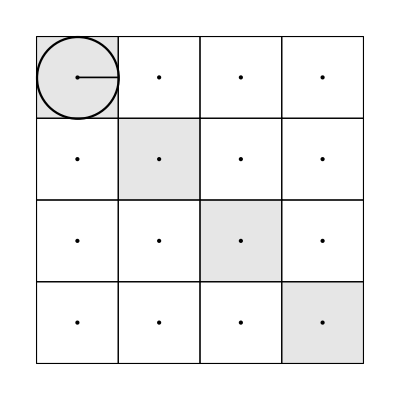
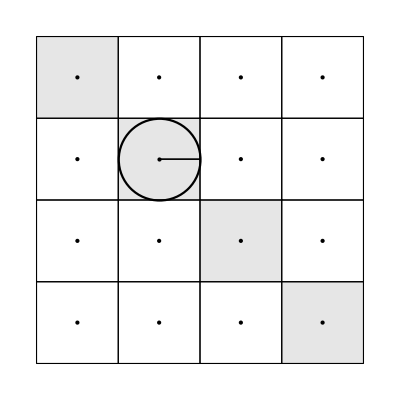
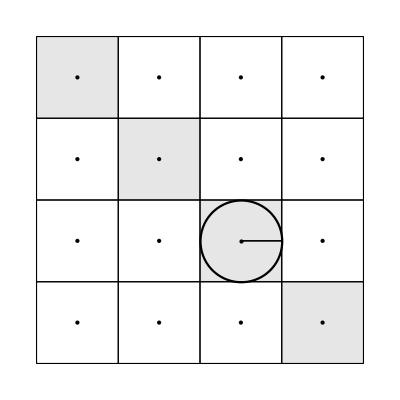
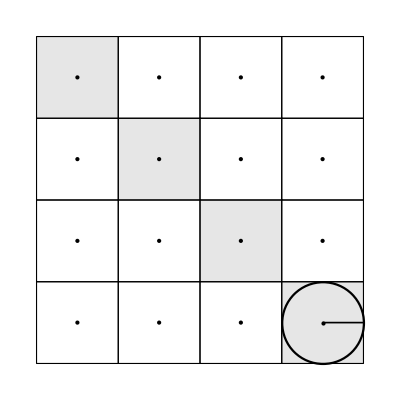

```mathematica
idealStates3=Table[(-1)^KroneckerDelta[i,j],{i,1,4},{j,1,4}]/2;
idealStates5=Table[KroneckerDelta[i,j],{i,1,4},{j,1,4}];
MatrixForm/@(idealMatrices3=KroneckerProduct[#,#]&/@idealStates3)
MatrixForm/@(idealMatrices5=KroneckerProduct[#,#]&/@idealStates5)
opts0={
borderColor->Black,arrowColor->Black,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.004, thicknessArrow->0.003,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&),
showCentralPoint->True ,centralPointSize->Medium};
idealGraphs3=ComplexMatrixDraw[#,Sequence @@ opts0]&/@idealMatrices3
idealGraphs5=ComplexMatrixDraw[#,Sequence @@ opts0]&/@idealMatrices5
```

#### Import measured density matrices

```mathematica
myImport[fileName_]:=
Block[{data=Import[fileName,"Table"],header},
header=Take[data,1]//Flatten//ToExpression;
data=Flatten[Drop[data,1]];
MapThread[#1->#2&,{header,data}]
]
```

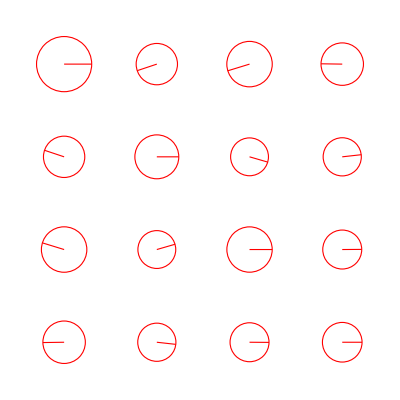
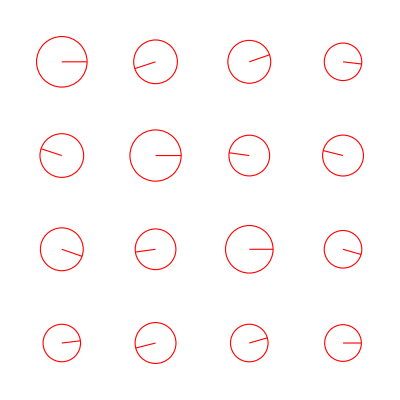
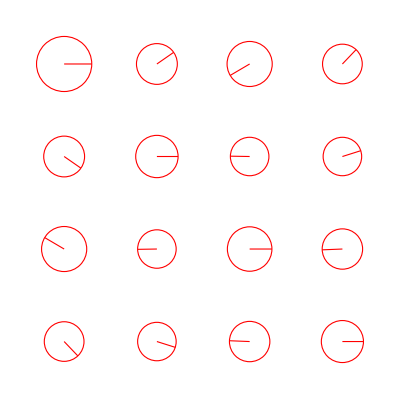
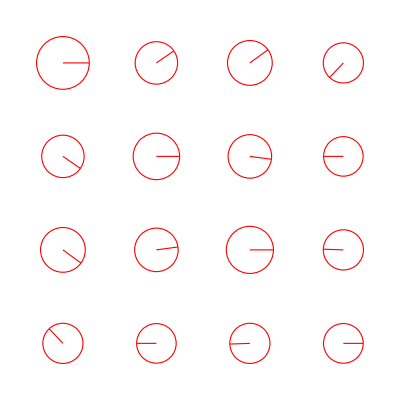

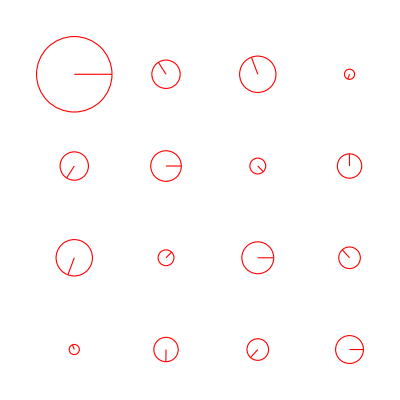
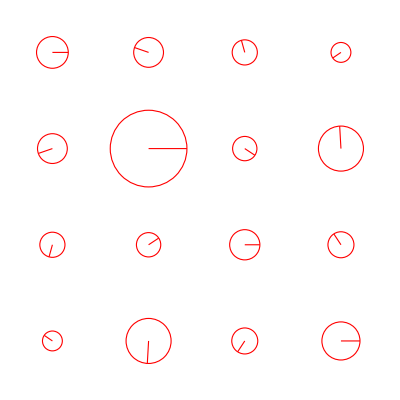
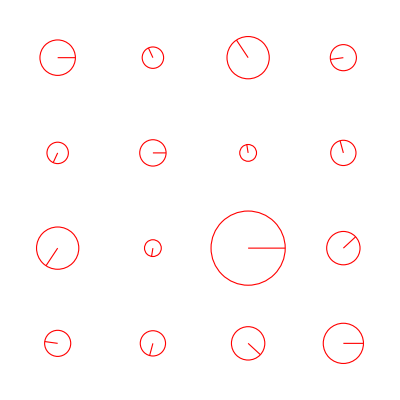
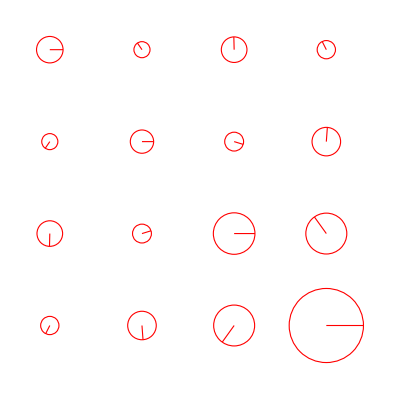

```mathematica
measuredPauliSets3=myImport[path<>baseName<>#<>ext]&/@endNames3;
measuredPauliSets5=myImport[path<>baseName<>#<>ext]&/@endNames5;
path="L:\\local-expdata\\FO-C5\\3rd-Run\\2011_04_21\\good_data\\";
baseName="Grover Search Algorithm-1-State = ";
ext=".txt";
endNames3={"0 - Step = 3-2-spins-0","1 - Step = 3-7-spins-0","2 - Step = 3-12-spins-0","3 - Step = 3-17-spins-0"};
endNames5={"0 - Step = 5-4-spins-0","1 - Step = 5-9-spins-0","2 - Step = 5-14-spins-0","3 - Step = 5-19-spins-0"};
measuredPauliSets3=myImport[path<>baseName<>#<>ext]&/@endNames3;
measuredPauliSets5=myImport[path<>baseName<>#<>ext]&/@endNames5;
tomos3=(ρS/.#)&/@measuredPauliSets3;
tomos5=(ρS/.#)&/@measuredPauliSets5;
MatrixForm/@tomos3;
MatrixForm/@tomos5;
opts1={
drawFrame->False,borderColor->Red,arrowColor->Red,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.002, thicknessArrow->0.002,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)};
tomoGraphs3=ComplexMatrixDraw[#,Sequence @@ opts1]&/@tomos3
tomoGraphs5=ComplexMatrixDraw[#,Sequence @@ opts1]&/@tomos5
```

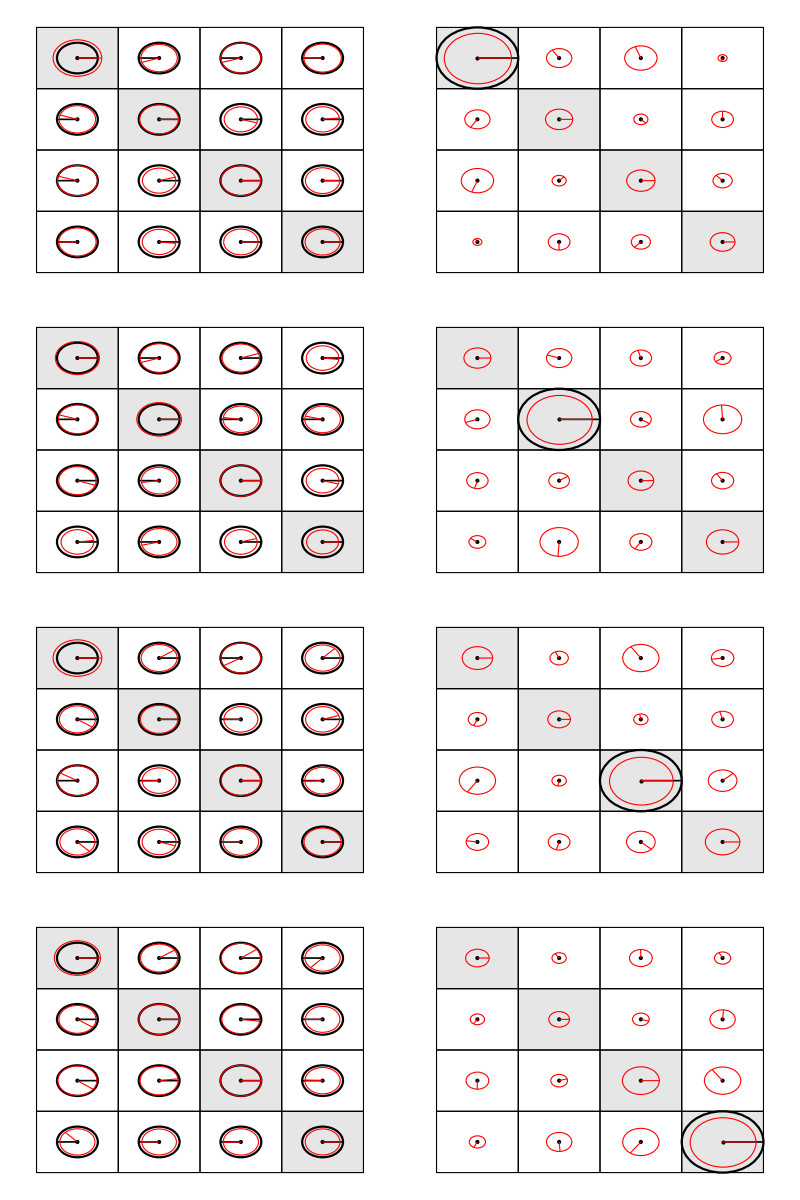
(-Graphics-)

```mathematica
graphs3=MapThread[Show[#1,#2]&,{idealGraphs3,tomoGraphs3}];
graphs5=MapThread[Show[#1,#2]&,{idealGraphs5,tomoGraphs5}];
Transpose[{graphs3,graphs5}]//MatrixForm
```